```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Lead=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{{0.-0.0000823223 ⅈ,-0.573223+0. ⅈ,0.+0.000025 ⅈ,0.25+0. ⅈ,0.-2.8033×10^-13 ⅈ,-0.0732233+0. ⅈ,0.-7.32233×10^-6 ⅈ,0.0732233+0. ⅈ,0.+0.0000146447 ⅈ,-0.176777+0. ⅈ,0.-0.0000323223 ⅈ,0.323223+0. ⅈ,0.+0.0000396447 ⅈ,-0.426777+0. ⅈ},12,{-0.426777+0. ⅈ,0.+1035.53 ⅈ,0.323223+0. ⅈ,0.-1464.47 ⅈ,-0.176777+0. ⅈ,0.+1035.53 ⅈ,0.0732233+0. ⅈ,0.-1,0.0303301+0. ⅈ,0.+428.932 ⅈ,0.103553+0. ⅈ,0.+428.932 ⅈ,-0.46967+0. ⅈ,0.-1035.53 ⅈ}},299,{1}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[ω*100+1]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

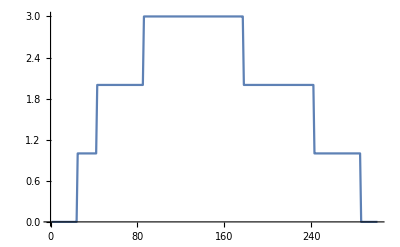

```mathematica
ListLinePlot[ParallelTable[tr[ω,0.0001,1,0],{ω,0,3,0.01}]]
```

```mathematica
Tan[60]
```

Tan[60]

```mathematica
N[Tan[π/3]]
```

1.73205

```mathematica
Cos[π/6]
```

(√3)/2

```mathematica
Sin[π/3]/Cos[π/3]
```

√3

```mathematica
N[Sin[60]]
```

-0.304811

```mathematica
RandomSample[Join[Flatten[Table[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],3 ]],Table[imp,58]]]
```

{imp,imp,imp,imp,imp12,imp,imp1,imp,imp7,imp,imp,imp,imp8,imp,imp4,imp11,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp12,imp,imp8,imp6,imp,imp10,imp,imp3,imp14,imp7,imp,imp,imp5,imp,imp2,imp14,imp3,imp,imp2,imp,imp,imp12,imp1,imp9,imp10,imp,imp,imp5,imp11,imp,imp,imp,imp6,imp,imp5,imp,imp,imp,imp,imp3,imp9,imp1,imp,imp9,imp4,imp10,imp2,imp,imp13,imp,imp,imp,imp,imp,imp,imp,imp,imp14,imp6,imp7,imp,imp,imp,imp,imp11,imp8,imp,imp4,imp,imp,imp,imp,imp13,imp,imp13}

```mathematica
f[y_]:=Table[{x,y},{x,Range[0,3,0.5]}]
```

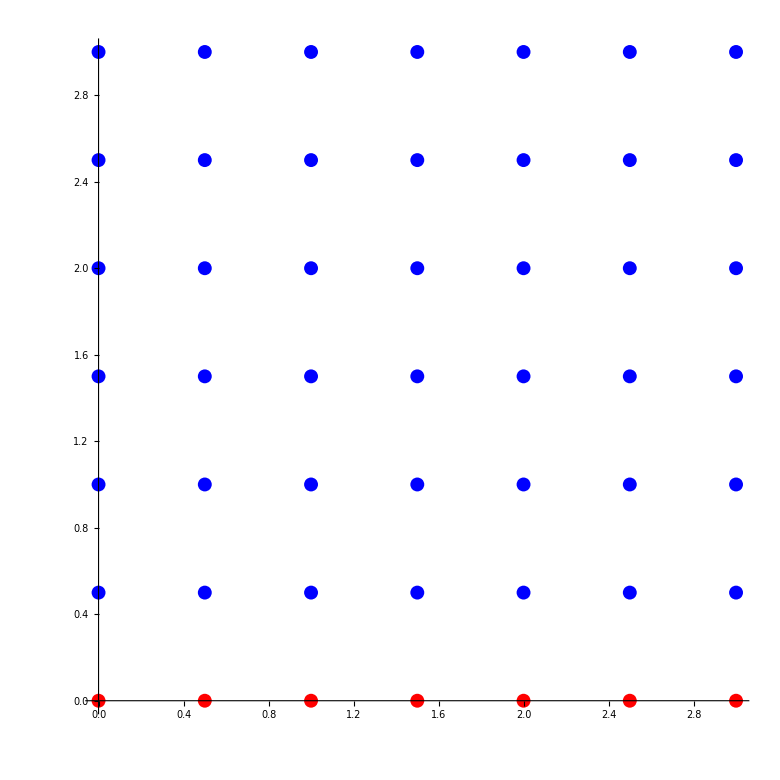

```mathematica
Show[ListPlot[f[0.0],PlotStyle->Red],ListPlot[f[0.5],PlotStyle->Blue],ListPlot[f[01],PlotStyle->Blue],ListPlot[f[1.5],PlotStyle->Blue],ListPlot[f[2.0],PlotStyle->Blue],ListPlot[f[2.5],PlotStyle->Blue],ListPlot[f[3.0],PlotStyle->Blue],PlotRange->All,AspectRatio->1]
```

```mathematica
Tally[{imp,imp,imp4,imp,imp,imp6,imp,imp1,imp7,imp,imp4,imp4,imp,imp3,imp7,imp5,imp,imp,imp3,imp,imp,imp,imp,imp,imp3,imp1,imp2,imp5,imp,imp4,imp4,imp2,imp,imp5,imp,imp,imp,imp,imp,imp,imp6,imp,imp,imp,imp,imp1,imp6,imp,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp6,imp,imp1,imp,imp3,imp,imp,imp,imp,imp,imp,imp,imp7,imp,imp,imp,imp,imp,imp5,imp,imp,imp6,imp1,imp,imp2,imp3,imp,imp,imp,imp,imp,imp7,imp,imp,imp,imp,imp,imp,imp5,imp,imp,imp7,imp2}]
```

{{imp,65},{imp4,5},{imp6,5},{imp1,5},{imp7,5},{imp3,5},{imp5,5},{imp2,5}}

```mathematica
m14[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ2]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ2]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ2]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ2]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001]]]},
lista={RandomSample[{imp9,imp,imp,imp,imp3,imp,imp,imp14,imp4,imp,imp5,imp,imp,imp,imp,imp,imp,imp,imp,imp3,imp,imp,imp,imp11,imp,imp,imp,imp,imp2,imp6,imp6,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp13,imp,imp,imp,imp,imp8,imp2,imp11,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp7,imp,imp12,imp5,imp,imp,imp,imp,imp,imp,imp,imp,imp1,imp8,imp,imp1,imp,imp,imp,imp,imp10,imp,imp10,imp14,imp,imp,imp,imp,imp4,imp13,imp,imp,imp,imp9,imp,imp,imp7,imp12,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
m1414= Compile[{ω,ϵ1,ϵ2},m14[ω,ϵ1,ϵ2],CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
Mean[ParallelTable[m1414[1,0.1,0.9],2000]]//AbsoluteTiming
```

{28.5396,1.67874}

```mathematica
Table[{ω,Mean[ParallelTable[m1414[ω,0.1,0.9],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,1.33651×10^-6},{0.01,7.24607×10^-6},{0.02,8.29561×10^-6},{0.03,0.0000101518},{0.04,0.0000169117},{0.05,0.0000259919},{0.06,0.0000292762},{0.07,0.0000376818},{0.08,0.0000622508},{0.09,0.0000770332},{0.1,0.0000810464},{0.11,0.0000934538},{0.12,0.000147558},{0.13,0.000161604},{0.14,0.000228284},{0.15,0.000268958},{0.16,0.000295451},{0.17,0.000318965},{0.18,0.0005499},{0.19,0.000461079},{0.2,0.00109679},{0.21,0.00127359},{0.22,0.00219352},{0.23,0.00608599},{0.24,0.173562},{0.25,0.251577},{0.26,0.35363},{0.27,0.427382},{0.28,0.479378},{0.29,0.537171},{0.3,0.571424},{0.31,0.599675},{0.32,0.612347},{0.33,0.629757},{0.34,0.653691},{0.35,0.67164},{0.36,0.669724},{0.37,0.684372},{0.38,0.682239},{0.39,0.679675},{0.4,0.668925},{0.41,0.622615},{0.42,1.26957},{0.43,1.04124},{0.44,0.794698},{0.45,0.691643},{0.46,0.705868},{0.47,0.731628},{0.48,0.795558},{0.49,0.833259},{0.5,0.867092},{0.51,0.913955},{0.52,0.955848},{0.53,0.989038},{0.54,1.02682},{0.55,1.06324},{0.56,1.08118},{0.57,1.10962},{0.58,1.11628},{0.59,1.14132},{0.6,1.16854},{0.61,1.18652},{0.62,1.21496},{0.63,1.20601},{0.64,1.21921},{0.65,1.24855},{0.66,1.26164},{0.67,1.27487},{0.68,1.28338},{0.69,1.29372},{0.7,1.31728},{0.71,1.31818},{0.72,1.33491},{0.73,1.35183},{0.74,1.34958},{0.75,1.36092},{0.76,1.37501},{0.77,1.37525},{0.78,1.40121},{0.79,1.42009},{0.8,1.42928},{0.81,1.43819},{0.82,1.45289},{0.83,1.45624},{0.84,1.42395},{0.85,1.19731},{0.86,1.08913},{0.87,0.871784},{0.88,0.876575},{0.89,0.968622},{0.9,1.09773},{0.91,1.18755},{0.92,1.28499},{0.93,1.35919},{0.94,1.43223},{0.95,1.49027},{0.96,1.55685},{0.97,1.61908},{0.98,1.6517},{0.99,1.69219},{1.,1.6952},{1.01,1.68906},{1.02,1.69166},{1.03,1.69555},{1.04,1.59165},{1.05,1.45257},{1.06,1.24531},{1.07,0.987215},{1.08,0.727641},{1.09,0.521286},{1.1,0.396757},{1.11,0.369731},{1.12,0.358327},{1.13,0.371659},{1.14,0.398992},{1.15,0.438954},{1.16,0.475927},{1.17,0.526031},{1.18,0.550205},{1.19,0.609151},{1.2,0.671988},{1.21,0.706615},{1.22,0.758926},{1.23,0.783282},{1.24,0.82166},{1.25,0.851041},{1.26,0.894598},{1.27,0.873372},{1.28,0.90459},{1.29,0.933828},{1.3,0.945443},{1.31,0.958191},{1.32,0.973809},{1.33,0.972097},{1.34,0.981283},{1.35,1.00279},{1.36,1.00523},{1.37,1.00478},{1.38,1.03178},{1.39,1.02629},{1.4,1.0264},{1.41,1.02922},{1.42,1.04179},{1.43,1.05268},{1.44,1.03824},{1.45,0.979621},{1.46,0.985788},{1.47,1.0083},{1.48,0.998167},{1.49,0.987861},{1.5,0.986345},{1.51,0.979665},{1.52,0.977347},{1.53,0.962629},{1.54,0.973525},{1.55,0.963303},{1.56,0.868747},{1.57,0.887603},{1.58,0.898258},{1.59,0.866872},{1.6,0.854823},{1.61,0.852409},{1.62,0.823323},{1.63,0.825973},{1.64,0.780623},{1.65,0.756762},{1.66,0.749475},{1.67,0.700155},{1.68,0.66276},{1.69,0.640567},{1.7,0.618527},{1.71,0.619349},{1.72,0.618559},{1.73,0.60911},{1.74,0.680958},{1.75,0.852529},{1.76,1.65002},{1.77,2.06235},{1.78,1.16671},{1.79,0.909232},{1.8,0.890153},{1.81,0.85639},{1.82,0.803923},{1.83,0.832244},{1.84,0.642654},{1.85,0.605949},{1.86,0.540603},{1.87,0.527799},{1.88,0.558843},{1.89,0.570616},{1.9,0.580188},{1.91,0.571865},{1.92,0.59213},{1.93,0.615458},{1.94,0.652618},{1.95,0.654206},{1.96,0.681639},{1.97,0.685325},{1.98,0.712696},{1.99,0.712842},{2.,0.711238},{2.01,0.719099},{2.02,0.731116},{2.03,0.728207},{2.04,0.74933},{2.05,0.727678},{2.06,0.729429},{2.07,0.728265},{2.08,0.736551},{2.09,0.731316},{2.1,0.730389},{2.11,0.680662},{2.12,0.66582},{2.13,0.701548},{2.14,0.68135},{2.15,0.683447},{2.16,0.704832},{2.17,0.681382},{2.18,0.6814},{2.19,0.67276},{2.2,0.657903},{2.21,0.654067},{2.22,0.63755},{2.23,0.627957},{2.24,0.605907},{2.25,0.603979},{2.26,0.59399},{2.27,0.573648},{2.28,0.562802},{2.29,0.540419},{2.3,0.509142},{2.31,0.500454},{2.32,0.497084},{2.33,0.467159},{2.34,0.447965},{2.35,0.439129},{2.36,0.420329},{2.37,0.415914},{2.38,0.396443},{2.39,0.411709},{2.4,0.463527},{2.41,0.707531},{2.42,0.828346},{2.43,0.860069},{2.44,1.49958},{2.45,0.587156},{2.46,0.567195},{2.47,0.547939},{2.48,0.453817},{2.49,0.265106},{2.5,0.250988},{2.51,0.265713},{2.52,0.224773},{2.53,0.22948},{2.54,0.238438},{2.55,0.239835},{2.56,0.24592},{2.57,0.25096},{2.58,0.253982},{2.59,0.259804},{2.6,0.259261},{2.61,0.246224},{2.62,0.257835},{2.63,0.25556},{2.64,0.2541},{2.65,0.241707},{2.66,0.236429},{2.67,0.235077},{2.68,0.235403},{2.69,0.226914},{2.7,0.218864},{2.71,0.210133},{2.72,0.213142},{2.73,0.201817},{2.74,0.189436},{2.75,0.18304},{2.76,0.179714},{2.77,0.168032},{2.78,0.163199},{2.79,0.148078},{2.8,0.153542},{2.81,0.145645},{2.82,0.131194},{2.83,0.138738},{2.84,0.134806},{2.85,0.666838},{2.86,0.042872},{2.87,0.160434},{2.88,0.0749235},{2.89,0.0167224},{2.9,0.128524},{2.91,0.113686},{2.92,0.0132577},{2.93,0.00022387},{2.94,0.0011487},{2.95,0.000766715},{2.96,0.00105488},{2.97,0.000499601},{2.98,0.000180933},{2.99,0.000353224},{3.,0.000264859}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/2per/m141403.dat",%51]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/2per/m141403.dat

```mathematica
Table[{ω,Mean[ParallelTable[m1414[ω,0.3,0.9],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,3.05381×10^-6},{0.01,4.16287×10^-6},{0.02,6.53866×10^-6},{0.03,8.64125×10^-6},{0.04,0.0000158099},{0.05,0.0000211859},{0.06,0.0000283625},{0.07,0.0000445088},{0.08,0.0000580373},{0.09,0.0000711874},{0.1,0.0000802275},{0.11,0.0000986152},{0.12,0.000125199},{0.13,0.000168709},{0.14,0.000176857},{0.15,0.000271745},{0.16,0.000319033},{0.17,0.000358772},{0.18,0.000398337},{0.19,0.00054291},{0.2,0.000746224},{0.21,0.00135261},{0.22,0.00256655},{0.23,0.00548231},{0.24,0.12103},{0.25,0.220027},{0.26,0.305933},{0.27,0.383406},{0.28,0.456947},{0.29,0.504494},{0.3,0.533635},{0.31,0.568781},{0.32,0.588572},{0.33,0.604688},{0.34,0.60695},{0.35,0.629266},{0.36,0.641967},{0.37,0.651258},{0.38,0.658905},{0.39,0.655008},{0.4,0.633564},{0.41,0.570066},{0.42,1.20915},{0.43,1.14367},{0.44,0.847124},{0.45,0.698653},{0.46,0.668727},{0.47,0.684266},{0.48,0.699988},{0.49,0.748597},{0.5,0.81806},{0.51,0.835964},{0.52,0.886113},{0.53,0.917658},{0.54,0.964529},{0.55,0.982759},{0.56,1.00263},{0.57,1.04324},{0.58,1.06133},{0.59,1.07519},{0.6,1.11726},{0.61,1.13007},{0.62,1.13547},{0.63,1.16553},{0.64,1.17491},{0.65,1.18075},{0.66,1.19525},{0.67,1.2206},{0.68,1.21712},{0.69,1.24474},{0.7,1.26472},{0.71,1.25523},{0.72,1.2719},{0.73,1.2883},{0.74,1.28867},{0.75,1.31985},{0.76,1.31832},{0.77,1.32552},{0.78,1.34379},{0.79,1.34833},{0.8,1.35922},{0.81,1.3698},{0.82,1.37802},{0.83,1.36993},{0.84,1.34559},{0.85,1.06997},{0.86,1.15171},{0.87,0.839544},{0.88,0.822329},{0.89,0.887282},{0.9,0.947735},{0.91,1.05961},{0.92,1.13972},{0.93,1.21251},{0.94,1.29523},{0.95,1.35644},{0.96,1.44274},{0.97,1.47566},{0.98,1.54491},{0.99,1.53292},{1.,1.5665},{1.01,1.69374},{1.02,1.59627},{1.03,1.09808},{1.04,0.43103},{1.05,0.851378},{1.06,0.943901},{1.07,0.823176},{1.08,0.644598},{1.09,0.479113},{1.1,0.381982},{1.11,0.350023},{1.12,0.355194},{1.13,0.369368},{1.14,0.374006},{1.15,0.400614},{1.16,0.435274},{1.17,0.495358},{1.18,0.535202},{1.19,0.581844},{1.2,0.614214},{1.21,0.670761},{1.22,0.694933},{1.23,0.736841},{1.24,0.760809},{1.25,0.794309},{1.26,0.83974},{1.27,0.83627},{1.28,0.845397},{1.29,0.873994},{1.3,0.887397},{1.31,0.898341},{1.32,0.905415},{1.33,0.921787},{1.34,0.936451},{1.35,0.931243},{1.36,0.93863},{1.37,0.948782},{1.38,0.949321},{1.39,0.933512},{1.4,0.929819},{1.41,0.965186},{1.42,0.94645},{1.43,0.959189},{1.44,0.951236},{1.45,0.916026},{1.46,0.906407},{1.47,0.899404},{1.48,0.921517},{1.49,0.912435},{1.5,0.906546},{1.51,0.890318},{1.52,0.894318},{1.53,0.878996},{1.54,0.86942},{1.55,0.874145},{1.56,0.810749},{1.57,0.808392},{1.58,0.793232},{1.59,0.795982},{1.6,0.77876},{1.61,0.760665},{1.62,0.732172},{1.63,0.706473},{1.64,0.702349},{1.65,0.679684},{1.66,0.650292},{1.67,0.624008},{1.68,0.591973},{1.69,0.597532},{1.7,0.570621},{1.71,0.564732},{1.72,0.581882},{1.73,0.600036},{1.74,0.702701},{1.75,0.959844},{1.76,1.87947},{1.77,4.06939},{1.78,1.35799},{1.79,0.938466},{1.8,0.886028},{1.81,0.924504},{1.82,0.867905},{1.83,0.801316},{1.84,0.616696},{1.85,0.5542},{1.86,0.542612},{1.87,0.524821},{1.88,0.539285},{1.89,0.549386},{1.9,0.551408},{1.91,0.552885},{1.92,0.537539},{1.93,0.585065},{1.94,0.611013},{1.95,0.631523},{1.96,0.648835},{1.97,0.657391},{1.98,0.67279},{1.99,0.661982},{2.,0.681023},{2.01,0.692295},{2.02,0.692951},{2.03,0.701397},{2.04,0.702389},{2.05,0.701712},{2.06,0.689149},{2.07,0.708837},{2.08,0.699284},{2.09,0.702269},{2.1,0.703068},{2.11,0.645979},{2.12,0.630955},{2.13,0.648539},{2.14,0.667624},{2.15,0.651473},{2.16,0.649314},{2.17,0.635616},{2.18,0.639569},{2.19,0.631113},{2.2,0.610268},{2.21,0.618252},{2.22,0.596771},{2.23,0.589706},{2.24,0.572497},{2.25,0.569033},{2.26,0.561432},{2.27,0.543293},{2.28,0.502546},{2.29,0.500726},{2.3,0.488123},{2.31,0.462575},{2.32,0.47191},{2.33,0.42542},{2.34,0.426107},{2.35,0.40028},{2.36,0.394069},{2.37,0.375362},{2.38,0.378798},{2.39,0.405886},{2.4,0.479494},{2.41,0.876424},{2.42,1.85678},{2.43,0.983193},{2.44,1.24927},{2.45,0.644104},{2.46,0.674989},{2.47,0.625862},{2.48,0.39449},{2.49,0.318643},{2.5,0.25188},{2.51,0.253058},{2.52,0.237799},{2.53,0.226044},{2.54,0.232701},{2.55,0.227028},{2.56,0.234748},{2.57,0.242552},{2.58,0.238286},{2.59,0.2384},{2.6,0.236549},{2.61,0.242926},{2.62,0.23682},{2.63,0.253022},{2.64,0.240051},{2.65,0.236431},{2.66,0.230589},{2.67,0.230405},{2.68,0.223338},{2.69,0.225416},{2.7,0.21476},{2.71,0.211853},{2.72,0.204493},{2.73,0.191095},{2.74,0.194925},{2.75,0.171139},{2.76,0.172745},{2.77,0.160105},{2.78,0.155292},{2.79,0.145347},{2.8,0.140921},{2.81,0.133488},{2.82,0.130219},{2.83,0.12821},{2.84,0.133358},{2.85,0.632189},{2.86,0.0897342},{2.87,0.382231},{2.88,0.0769994},{2.89,0.0095966},{2.9,0.0834472},{2.91,0.298427},{2.92,0.00297559},{2.93,0.000640662},{2.94,0.0138522},{2.95,0.000372007},{2.96,0.000326879},{2.97,0.000191295},{2.98,0.000319626},{2.99,0.000176355},{3.,0.000162964}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/2per/m141405.dat",%52]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/2per/m141405.dat

```mathematica
Table[{ω,Mean[ParallelTable[m1414[ω,0.5,0.9],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,1.11548×10^-6},{0.01,5.53186×10^-6},{0.02,8.54739×10^-6},{0.03,0.0000109865},{0.04,0.0000170235},{0.05,0.0000221967},{0.06,0.0000371007},{0.07,0.0000517738},{0.08,0.0000690902},{0.09,0.0000822474},{0.1,0.000105342},{0.11,0.000111937},{0.12,0.000152625},{0.13,0.000179451},{0.14,0.000205749},{0.15,0.000262254},{0.16,0.000320817},{0.17,0.00039843},{0.18,0.000514915},{0.19,0.000684047},{0.2,0.000781812},{0.21,0.00102041},{0.22,0.00199441},{0.23,0.00628386},{0.24,0.118074},{0.25,0.18227},{0.26,0.257162},{0.27,0.328538},{0.28,0.39795},{0.29,0.438513},{0.3,0.488595},{0.31,0.507237},{0.32,0.517303},{0.33,0.550033},{0.34,0.570016},{0.35,0.592815},{0.36,0.59505},{0.37,0.600312},{0.38,0.603701},{0.39,0.595049},{0.4,0.582198},{0.41,0.52986},{0.42,1.19647},{0.43,1.26476},{0.44,0.892821},{0.45,0.722137},{0.46,0.641021},{0.47,0.632144},{0.48,0.657871},{0.49,0.681957},{0.5,0.690432},{0.51,0.752486},{0.52,0.778408},{0.53,0.824071},{0.54,0.855849},{0.55,0.879557},{0.56,0.928897},{0.57,0.927996},{0.58,0.9505},{0.59,0.972864},{0.6,1.00063},{0.61,1.01808},{0.62,1.0394},{0.63,1.05595},{0.64,1.06933},{0.65,1.08668},{0.66,1.1012},{0.67,1.12092},{0.68,1.11269},{0.69,1.14898},{0.7,1.16676},{0.71,1.17204},{0.72,1.17042},{0.73,1.17197},{0.74,1.20381},{0.75,1.22223},{0.76,1.21812},{0.77,1.23059},{0.78,1.24699},{0.79,1.2678},{0.8,1.26654},{0.81,1.28089},{0.82,1.28495},{0.83,1.285},{0.84,1.22179},{0.85,1.07378},{0.86,1.19922},{0.87,0.893458},{0.88,0.782158},{0.89,0.772758},{0.9,0.818185},{0.91,0.898157},{0.92,0.97908},{0.93,1.04046},{0.94,1.13893},{0.95,1.18541},{0.96,1.26687},{0.97,1.33472},{0.98,1.3893},{0.99,1.40323},{1.,1.42955},{1.01,1.55156},{1.02,1.46494},{1.03,1.36811},{1.04,1.10005},{1.05,0.657347},{1.06,0.39012},{1.07,0.358113},{1.08,0.387378},{1.09,0.364154},{1.1,0.355745},{1.11,0.332998},{1.12,0.338719},{1.13,0.344849},{1.14,0.349601},{1.15,0.374482},{1.16,0.397854},{1.17,0.433323},{1.18,0.464093},{1.19,0.502277},{1.2,0.542642},{1.21,0.563846},{1.22,0.590052},{1.23,0.636083},{1.24,0.686282},{1.25,0.673111},{1.26,0.689333},{1.27,0.719899},{1.28,0.724002},{1.29,0.742839},{1.3,0.757569},{1.31,0.767246},{1.32,0.789062},{1.33,0.783083},{1.34,0.791228},{1.35,0.799966},{1.36,0.808366},{1.37,0.818554},{1.38,0.807968},{1.39,0.819455},{1.4,0.813616},{1.41,0.801485},{1.42,0.819784},{1.43,0.829757},{1.44,0.82476},{1.45,0.779688},{1.46,0.764871},{1.47,0.775375},{1.48,0.782367},{1.49,0.766052},{1.5,0.76802},{1.51,0.755237},{1.52,0.744951},{1.53,0.753135},{1.54,0.733218},{1.55,0.71938},{1.56,0.658142},{1.57,0.651873},{1.58,0.661293},{1.59,0.661176},{1.6,0.636165},{1.61,0.625423},{1.62,0.616442},{1.63,0.593227},{1.64,0.603304},{1.65,0.562171},{1.66,0.555123},{1.67,0.533554},{1.68,0.526066},{1.69,0.515487},{1.7,0.517351},{1.71,0.539278},{1.72,0.553682},{1.73,0.614586},{1.74,0.746549},{1.75,1.061},{1.76,2.08389},{1.77,2.9674},{1.78,2.50358},{1.79,1.546},{1.8,1.15274},{1.81,0.897365},{1.82,0.807127},{1.83,0.692632},{1.84,0.615222},{1.85,0.582296},{1.86,0.4458},{1.87,0.46323},{1.88,0.489688},{1.89,0.492824},{1.9,0.492454},{1.91,0.496939},{1.92,0.492511},{1.93,0.525258},{1.94,0.550609},{1.95,0.563615},{1.96,0.558299},{1.97,0.578216},{1.98,0.5869},{1.99,0.605194},{2.,0.615851},{2.01,0.611061},{2.02,0.617051},{2.03,0.620165},{2.04,0.626846},{2.05,0.629421},{2.06,0.617791},{2.07,0.625392},{2.08,0.628144},{2.09,0.62334},{2.1,0.610838},{2.11,0.568559},{2.12,0.556791},{2.13,0.577011},{2.14,0.574676},{2.15,0.571722},{2.16,0.569023},{2.17,0.560393},{2.18,0.556998},{2.19,0.557546},{2.2,0.537698},{2.21,0.529937},{2.22,0.521923},{2.23,0.515746},{2.24,0.487907},{2.25,0.487109},{2.26,0.485841},{2.27,0.468162},{2.28,0.457513},{2.29,0.426003},{2.3,0.408746},{2.31,0.405195},{2.32,0.389949},{2.33,0.38437},{2.34,0.367798},{2.35,0.362614},{2.36,0.337138},{2.37,0.349884},{2.38,0.346728},{2.39,0.390808},{2.4,0.46907},{2.41,0.952271},{2.42,2.03336},{2.43,2.44189},{2.44,1.30725},{2.45,0.747311},{2.46,0.769602},{2.47,1.7288},{2.48,0.4354},{2.49,0.345036},{2.5,0.291862},{2.51,0.215256},{2.52,0.218152},{2.53,0.205801},{2.54,0.206341},{2.55,0.208389},{2.56,0.207364},{2.57,0.211163},{2.58,0.223919},{2.59,0.216705},{2.6,0.214267},{2.61,0.215272},{2.62,0.208525},{2.63,0.219555},{2.64,0.208661},{2.65,0.212207},{2.66,0.201167},{2.67,0.209689},{2.68,0.202712},{2.69,0.199273},{2.7,0.190024},{2.71,0.18158},{2.72,0.165655},{2.73,0.162224},{2.74,0.168411},{2.75,0.163156},{2.76,0.144614},{2.77,0.147005},{2.78,0.141285},{2.79,0.136449},{2.8,0.132662},{2.81,0.126035},{2.82,0.115959},{2.83,0.119572},{2.84,0.135874},{2.85,2.75909},{2.86,2.06126},{2.87,0.131103},{2.88,0.257933},{2.89,0.0107811},{2.9,0.186394},{2.91,0.013947},{2.92,0.005242},{2.93,0.00113907},{2.94,0.00159219},{2.95,0.00103313},{2.96,0.000209505},{2.97,0.000350397},{2.98,0.000189978},{2.99,0.000344266},{3.,0.000224057}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/2per/m141407.dat",%53]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/2per/m141407.dat

```mathematica
Table[{ω,Mean[ParallelTable[m1414[ω,0.7,0.9],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,5.14857×10^-6},{0.01,0.000012445},{0.02,8.56086×10^-6},{0.03,0.0000123246},{0.04,0.0000198572},{0.05,0.0000275319},{0.06,0.0000390587},{0.07,0.0000485817},{0.08,0.0000762538},{0.09,0.0000840366},{0.1,0.000125931},{0.11,0.000145363},{0.12,0.000167394},{0.13,0.000177646},{0.14,0.000237655},{0.15,0.000285588},{0.16,0.000371104},{0.17,0.000465276},{0.18,0.000409121},{0.19,0.000754955},{0.2,0.00107256},{0.21,0.00142603},{0.22,0.00254181},{0.23,0.00591686},{0.24,0.109179},{0.25,0.165483},{0.26,0.227948},{0.27,0.280273},{0.28,0.331049},{0.29,0.381885},{0.3,0.416777},{0.31,0.450097},{0.32,0.475794},{0.33,0.498283},{0.34,0.514979},{0.35,0.526093},{0.36,0.540251},{0.37,0.545233},{0.38,0.542507},{0.39,0.544904},{0.4,0.535512},{0.41,0.497171},{0.42,1.16936},{0.43,1.29227},{0.44,1.01037},{0.45,0.781789},{0.46,0.643592},{0.47,0.599667},{0.48,0.59483},{0.49,0.61299},{0.5,0.631611},{0.51,0.649128},{0.52,0.67204},{0.53,0.708019},{0.54,0.743176},{0.55,0.765898},{0.56,0.787699},{0.57,0.822182},{0.58,0.846324},{0.59,0.857319},{0.6,0.885695},{0.61,0.909682},{0.62,0.93034},{0.63,0.937544},{0.64,0.965551},{0.65,0.97706},{0.66,0.993514},{0.67,1.00273},{0.68,1.01455},{0.69,1.02778},{0.7,1.04996},{0.71,1.05556},{0.72,1.05587},{0.73,1.07926},{0.74,1.09299},{0.75,1.11131},{0.76,1.12605},{0.77,1.12308},{0.78,1.14393},{0.79,1.16407},{0.8,1.16385},{0.81,1.17323},{0.82,1.18181},{0.83,1.18134},{0.84,1.1255},{0.85,1.13689},{0.86,1.29322},{0.87,0.99056},{0.88,0.753274},{0.89,0.714096},{0.9,0.728269},{0.91,0.756939},{0.92,0.848037},{0.93,0.878094},{0.94,0.960931},{0.95,1.03141},{0.96,1.09042},{0.97,1.12005},{0.98,1.17484},{0.99,1.21762},{1.,1.23874},{1.01,1.36243},{1.02,1.31021},{1.03,1.24831},{1.04,1.11607},{1.05,0.892671},{1.06,0.627614},{1.07,0.421137},{1.08,0.341241},{1.09,0.319026},{1.1,0.333176},{1.11,0.333313},{1.12,0.32225},{1.13,0.313563},{1.14,0.324514},{1.15,0.33194},{1.16,0.344513},{1.17,0.356674},{1.18,0.376137},{1.19,0.404623},{1.2,0.425874},{1.21,0.456405},{1.22,0.488118},{1.23,0.498701},{1.24,0.510105},{1.25,0.536004},{1.26,0.570574},{1.27,0.568152},{1.28,0.572784},{1.29,0.599177},{1.3,0.607199},{1.31,0.597298},{1.32,0.624074},{1.33,0.629327},{1.34,0.641091},{1.35,0.643075},{1.36,0.663678},{1.37,0.646433},{1.38,0.659951},{1.39,0.672468},{1.4,0.658486},{1.41,0.651514},{1.42,0.662648},{1.43,0.66162},{1.44,0.655872},{1.45,0.640922},{1.46,0.609021},{1.47,0.633748},{1.48,0.625279},{1.49,0.632171},{1.5,0.620865},{1.51,0.598831},{1.52,0.620241},{1.53,0.609129},{1.54,0.602682},{1.55,0.589626},{1.56,0.559548},{1.57,0.520405},{1.58,0.540952},{1.59,0.537713},{1.6,0.536356},{1.61,0.519746},{1.62,0.511665},{1.63,0.502358},{1.64,0.488259},{1.65,0.47966},{1.66,0.478336},{1.67,0.460537},{1.68,0.472244},{1.69,0.47584},{1.7,0.490442},{1.71,0.517761},{1.72,0.549035},{1.73,0.64781},{1.74,0.81517},{1.75,1.18931},{1.76,2.19146},{1.77,2.94376},{1.78,1.77061},{1.79,1.71451},{1.8,1.66625},{1.81,1.44229},{1.82,1.21655},{1.83,0.886468},{1.84,0.733063},{1.85,0.577427},{1.86,0.458265},{1.87,0.436546},{1.88,0.422328},{1.89,0.414527},{1.9,0.392294},{1.91,0.409356},{1.92,0.393824},{1.93,0.430482},{1.94,0.44981},{1.95,0.467813},{1.96,0.471856},{1.97,0.472162},{1.98,0.495139},{1.99,0.494985},{2.,0.49162},{2.01,0.510928},{2.02,0.507411},{2.03,0.503553},{2.04,0.502108},{2.05,0.51229},{2.06,0.51006},{2.07,0.512121},{2.08,0.504927},{2.09,0.511131},{2.1,0.505034},{2.11,0.481021},{2.12,0.461893},{2.13,0.472918},{2.14,0.471248},{2.15,0.466413},{2.16,0.461395},{2.17,0.467027},{2.18,0.457763},{2.19,0.450053},{2.2,0.44898},{2.21,0.445976},{2.22,0.431658},{2.23,0.437128},{2.24,0.408794},{2.25,0.398124},{2.26,0.398784},{2.27,0.380598},{2.28,0.368105},{2.29,0.358759},{2.3,0.35831},{2.31,0.335032},{2.32,0.322091},{2.33,0.315809},{2.34,0.312094},{2.35,0.312141},{2.36,0.313239},{2.37,0.315716},{2.38,0.344604},{2.39,0.383028},{2.4,0.51389},{2.41,0.943842},{2.42,1.61527},{2.43,1.29605},{2.44,1.70608},{2.45,1.37592},{2.46,1.21974},{2.47,0.560346},{2.48,0.420482},{2.49,0.305266},{2.5,0.275789},{2.51,0.215692},{2.52,0.200647},{2.53,0.19383},{2.54,0.188891},{2.55,0.180716},{2.56,0.18351},{2.57,0.181072},{2.58,0.178069},{2.59,0.177665},{2.6,0.17929},{2.61,0.184702},{2.62,0.176404},{2.63,0.174148},{2.64,0.172403},{2.65,0.169336},{2.66,0.17659},{2.67,0.152499},{2.68,0.163251},{2.69,0.163153},{2.7,0.155938},{2.71,0.15191},{2.72,0.145737},{2.73,0.144019},{2.74,0.137802},{2.75,0.133163},{2.76,0.125029},{2.77,0.128973},{2.78,0.120104},{2.79,0.110958},{2.8,0.108441},{2.81,0.112157},{2.82,0.11352},{2.83,0.128376},{2.84,0.13705},{2.85,1.24686},{2.86,11.6622},{2.87,5.14878},{2.88,1.09974},{2.89,0.0115142},{2.9,0.123922},{2.91,0.00142139},{2.92,0.00572629},{2.93,0.00205508},{2.94,0.00052996},{2.95,0.000553023},{2.96,0.000525736},{2.97,0.000242726},{2.98,0.000248896},{2.99,0.000264609},{3.,0.000197052}}

```mathematica
m28[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ2]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ2]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ2]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ2]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001]]]},
lista={RandomSample[{imp,imp,imp,imp,imp5,imp,imp,imp,imp,imp,imp,imp,imp2,imp10,imp,imp,imp6,imp8,imp,imp,imp,imp,imp7,imp11,imp4,imp3,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp12,imp,imp,imp,imp9,imp,imp,imp,imp13,imp,imp4,imp,imp,imp,imp,imp14,imp,imp,imp,imp7,imp,imp,imp13,imp1,imp,imp,imp,imp,imp,imp,imp,imp6,imp,imp,imp,imp,imp,imp,imp10,imp,imp,imp1,imp,imp,imp,imp14,imp9,imp,imp,imp3,imp,imp8,imp2,imp12,imp,imp,imp,imp11,imp,imp,imp,imp,imp5}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
m2828= Compile[{ω,ϵ1,ϵ2},m28[ω,ϵ1,ϵ2],CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
Table[{ω,Mean[ParallelTable[m2828[ω,0.1,0.9],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[ParallelTable[m2828[ω,0.3,0.9],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[ParallelTable[m2828[ω,0.5,0.9],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[ParallelTable[m2828[ω,0.7,0.9],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,9.45228×10^-7},{0.01,8.2868×10^-6},{0.02,6.42407×10^-6},{0.03,0.0000129954},{0.04,0.0000173704},{0.05,0.0000243301},{0.06,0.000040844},{0.07,0.000039363},{0.08,0.0000502691},{0.09,0.0000638168},{0.1,0.0000951026},{0.11,0.000112859},{0.12,0.000119529},{0.13,0.000186341},{0.14,0.000178957},{0.15,0.000189415},{0.16,0.000392326},{0.17,0.000421965},{0.18,0.000530944},{0.19,0.000630185},{0.2,0.00084336},{0.21,0.00143792},{0.22,0.00212441},{0.23,0.00599654},{0.24,0.16081},{0.25,0.257999},{0.26,0.335836},{0.27,0.433863},{0.28,0.479395},{0.29,0.521806},{0.3,0.572233},{0.31,0.593449},{0.32,0.604452},{0.33,0.631263},{0.34,0.652977},{0.35,0.651684},{0.36,0.673342},{0.37,0.678527},{0.38,0.685185},{0.39,0.688682},{0.4,0.665931},{0.41,0.613552},{0.42,1.28163},{0.43,1.0446},{0.44,0.765601},{0.45,0.682429},{0.46,0.684069},{0.47,0.718549},{0.48,0.804725},{0.49,0.824832},{0.5,0.895414},{0.51,0.896938},{0.52,0.971877},{0.53,1.01036},{0.54,1.03211},{0.55,1.04886},{0.56,1.08692},{0.57,1.11661},{0.58,1.11691},{0.59,1.13764},{0.6,1.16366},{0.61,1.18923},{0.62,1.20443},{0.63,1.20544},{0.64,1.24207},{0.65,1.24147},{0.66,1.26577},{0.67,1.27063},{0.68,1.30354},{0.69,1.29523},{0.7,1.32221},{0.71,1.33102},{0.72,1.33189},{0.73,1.34111},{0.74,1.35526},{0.75,1.35786},{0.76,1.38083},{0.77,1.38817},{0.78,1.40611},{0.79,1.41894},{0.8,1.42886},{0.81,1.43738},{0.82,1.44086},{0.83,1.45644},{0.84,1.43135},{0.85,1.14466},{0.86,1.07976},{0.87,0.886186},{0.88,0.89532},{0.89,0.969795},{0.9,1.07127},{0.91,1.14593},{0.92,1.27647},{0.93,1.35132},{0.94,1.42529},{0.95,1.47872},{0.96,1.55491},{0.97,1.60479},{0.98,1.64158},{0.99,1.66819},{1.,1.68444},{1.01,1.68349},{1.02,1.67706},{1.03,1.68562},{1.04,1.60119},{1.05,1.44964},{1.06,1.25554},{1.07,0.990689},{1.08,0.716709},{1.09,0.521206},{1.1,0.412366},{1.11,0.369947},{1.12,0.365604},{1.13,0.375753},{1.14,0.392514},{1.15,0.427221},{1.16,0.45503},{1.17,0.509179},{1.18,0.568357},{1.19,0.624658},{1.2,0.672508},{1.21,0.705167},{1.22,0.734351},{1.23,0.779128},{1.24,0.82946},{1.25,0.871196},{1.26,0.885086},{1.27,0.879931},{1.28,0.921474},{1.29,0.931444},{1.3,0.935183},{1.31,0.954257},{1.32,0.995115},{1.33,0.972695},{1.34,0.97901},{1.35,0.999383},{1.36,1.01079},{1.37,0.99322},{1.38,1.01894},{1.39,1.02876},{1.4,1.02508},{1.41,1.0245},{1.42,1.04076},{1.43,1.03567},{1.44,1.03763},{1.45,0.966726},{1.46,0.978577},{1.47,0.99197},{1.48,0.988893},{1.49,0.993535},{1.5,0.985841},{1.51,0.984447},{1.52,0.982219},{1.53,0.961773},{1.54,0.975307},{1.55,0.940215},{1.56,0.854053},{1.57,0.874783},{1.58,0.878311},{1.59,0.873693},{1.6,0.858973},{1.61,0.832612},{1.62,0.80529},{1.63,0.799547},{1.64,0.771797},{1.65,0.752304},{1.66,0.723342},{1.67,0.689682},{1.68,0.661949},{1.69,0.664205},{1.7,0.627433},{1.71,0.605596},{1.72,0.605796},{1.73,0.626398},{1.74,0.672036},{1.75,0.863445},{1.76,1.64508},{1.77,2.06187},{1.78,1.19968},{1.79,0.972601},{1.8,0.963363},{1.81,0.938556},{1.82,0.96562},{1.83,0.752782},{1.84,0.70802},{1.85,0.569067},{1.86,0.549631},{1.87,0.555186},{1.88,0.561278},{1.89,0.571434},{1.9,0.592007},{1.91,0.562048},{1.92,0.592236},{1.93,0.608808},{1.94,0.636299},{1.95,0.659455},{1.96,0.673689},{1.97,0.698863},{1.98,0.691985},{1.99,0.715956},{2.,0.72564},{2.01,0.717828},{2.02,0.727284},{2.03,0.735884},{2.04,0.73271},{2.05,0.744729},{2.06,0.727146},{2.07,0.732783},{2.08,0.742776},{2.09,0.726194},{2.1,0.737367},{2.11,0.681312},{2.12,0.680823},{2.13,0.690697},{2.14,0.691079},{2.15,0.685088},{2.16,0.68291},{2.17,0.679755},{2.18,0.663815},{2.19,0.657576},{2.2,0.646448},{2.21,0.634995},{2.22,0.634167},{2.23,0.623112},{2.24,0.622676},{2.25,0.603822},{2.26,0.586949},{2.27,0.591576},{2.28,0.552687},{2.29,0.535876},{2.3,0.535253},{2.31,0.505301},{2.32,0.491635},{2.33,0.475819},{2.34,0.467681},{2.35,0.436045},{2.36,0.419321},{2.37,0.405081},{2.38,0.398349},{2.39,0.409314},{2.4,0.468107},{2.41,0.712172},{2.42,0.85082},{2.43,0.82426},{2.44,1.07332},{2.45,0.701743},{2.46,0.617436},{2.47,0.538751},{2.48,0.337629},{2.49,0.328337},{2.5,0.291425},{2.51,0.225602},{2.52,0.231136},{2.53,0.217762},{2.54,0.237535},{2.55,0.241766},{2.56,0.235348},{2.57,0.252194},{2.58,0.24832},{2.59,0.25165},{2.6,0.257986},{2.61,0.25537},{2.62,0.250014},{2.63,0.25344},{2.64,0.249058},{2.65,0.23735},{2.66,0.24161},{2.67,0.240413},{2.68,0.23051},{2.69,0.231195},{2.7,0.222642},{2.71,0.216651},{2.72,0.206631},{2.73,0.198385},{2.74,0.19272},{2.75,0.189347},{2.76,0.176434},{2.77,0.169887},{2.78,0.166132},{2.79,0.152936},{2.8,0.149221},{2.81,0.14147},{2.82,0.135771},{2.83,0.132939},{2.84,0.141211},{2.85,0.425001},{2.86,0.0475151},{2.87,0.755897},{2.88,0.072239},{2.89,0.0144362},{2.9,0.0210251},{2.91,0.00491679},{2.92,0.000509658},{2.93,0.000592765},{2.94,0.00050008},{2.95,0.000620677},{2.96,0.000574742},{2.97,0.000225429},{2.98,0.000417184},{2.99,0.000414068},{3.,0.0004414}}

{{0.,1.49029×10^-6},{0.01,2.80016×10^-6},{0.02,7.68721×10^-6},{0.03,8.93586×10^-6},{0.04,0.0000169665},{0.05,0.0000235935},{0.06,0.0000344381},{0.07,0.0000397701},{0.08,0.0000487137},{0.09,0.000074402},{0.1,0.000081162},{0.11,0.000114716},{0.12,0.000115232},{0.13,0.000155256},{0.14,0.000165555},{0.15,0.000298057},{0.16,0.000231795},{0.17,0.000384652},{0.18,0.000483945},{0.19,0.000490726},{0.2,0.000718974},{0.21,0.00120423},{0.22,0.0020895},{0.23,0.00567219},{0.24,0.130197},{0.25,0.21397},{0.26,0.319729},{0.27,0.38551},{0.28,0.44916},{0.29,0.497977},{0.3,0.540122},{0.31,0.563051},{0.32,0.576826},{0.33,0.60208},{0.34,0.608538},{0.35,0.633338},{0.36,0.63773},{0.37,0.644341},{0.38,0.652727},{0.39,0.64836},{0.4,0.639361},{0.41,0.582021},{0.42,1.18005},{0.43,1.14189},{0.44,0.834622},{0.45,0.712997},{0.46,0.654063},{0.47,0.683181},{0.48,0.719615},{0.49,0.76133},{0.5,0.804054},{0.51,0.836778},{0.52,0.887052},{0.53,0.921985},{0.54,0.975729},{0.55,0.981817},{0.56,1.01873},{0.57,1.04351},{0.58,1.06247},{0.59,1.0687},{0.6,1.11287},{0.61,1.12066},{0.62,1.15693},{0.63,1.16369},{0.64,1.17031},{0.65,1.18425},{0.66,1.19706},{0.67,1.21437},{0.68,1.21574},{0.69,1.23587},{0.7,1.25243},{0.71,1.26009},{0.72,1.26925},{0.73,1.28395},{0.74,1.29626},{0.75,1.30793},{0.76,1.3174},{0.77,1.33664},{0.78,1.3429},{0.79,1.35574},{0.8,1.36002},{0.81,1.37001},{0.82,1.38158},{0.83,1.39193},{0.84,1.3273},{0.85,1.10402},{0.86,1.15858},{0.87,0.873495},{0.88,0.816223},{0.89,0.862214},{0.9,0.956843},{0.91,1.0678},{0.92,1.12757},{0.93,1.20763},{0.94,1.30722},{0.95,1.37057},{0.96,1.42846},{0.97,1.51321},{0.98,1.54504},{0.99,1.56228},{1.,1.57255},{1.01,1.69567},{1.02,1.57257},{1.03,1.07591},{1.04,0.408307},{1.05,0.874674},{1.06,0.957957},{1.07,0.841815},{1.08,0.639009},{1.09,0.487391},{1.1,0.391926},{1.11,0.367129},{1.12,0.349167},{1.13,0.369658},{1.14,0.391663},{1.15,0.399084},{1.16,0.453269},{1.17,0.487289},{1.18,0.525548},{1.19,0.584745},{1.2,0.62985},{1.21,0.662163},{1.22,0.703687},{1.23,0.729776},{1.24,0.762718},{1.25,0.797792},{1.26,0.823872},{1.27,0.827341},{1.28,0.843545},{1.29,0.860004},{1.3,0.888859},{1.31,0.886617},{1.32,0.898276},{1.33,0.925672},{1.34,0.926341},{1.35,0.912783},{1.36,0.94824},{1.37,0.948716},{1.38,0.935667},{1.39,0.954378},{1.4,0.949039},{1.41,0.934681},{1.42,0.96138},{1.43,0.963888},{1.44,0.959871},{1.45,0.902463},{1.46,0.884684},{1.47,0.922189},{1.48,0.921703},{1.49,0.924275},{1.5,0.9092},{1.51,0.911111},{1.52,0.889668},{1.53,0.884161},{1.54,0.868373},{1.55,0.86249},{1.56,0.808119},{1.57,0.775902},{1.58,0.796631},{1.59,0.800987},{1.6,0.778319},{1.61,0.760096},{1.62,0.738924},{1.63,0.722011},{1.64,0.705594},{1.65,0.668235},{1.66,0.643814},{1.67,0.612428},{1.68,0.604342},{1.69,0.592165},{1.7,0.575425},{1.71,0.553793},{1.72,0.566398},{1.73,0.598999},{1.74,0.710913},{1.75,0.956311},{1.76,1.86437},{1.77,3.89301},{1.78,1.57836},{1.79,1.01738},{1.8,0.903473},{1.81,0.860618},{1.82,0.848421},{1.83,0.857053},{1.84,0.631195},{1.85,0.576364},{1.86,0.562062},{1.87,0.522501},{1.88,0.524116},{1.89,0.5554},{1.9,0.555959},{1.91,0.563516},{1.92,0.54877},{1.93,0.585737},{1.94,0.611755},{1.95,0.631923},{1.96,0.651531},{1.97,0.66464},{1.98,0.673075},{1.99,0.667418},{2.,0.688684},{2.01,0.696724},{2.02,0.702532},{2.03,0.704723},{2.04,0.695197},{2.05,0.705949},{2.06,0.701412},{2.07,0.708308},{2.08,0.693759},{2.09,0.698847},{2.1,0.695931},{2.11,0.636855},{2.12,0.63929},{2.13,0.644288},{2.14,0.648087},{2.15,0.641749},{2.16,0.65464},{2.17,0.63457},{2.18,0.637403},{2.19,0.62065},{2.2,0.605704},{2.21,0.613586},{2.22,0.599614},{2.23,0.58255},{2.24,0.561049},{2.25,0.560592},{2.26,0.545844},{2.27,0.536698},{2.28,0.523671},{2.29,0.495829},{2.3,0.484301},{2.31,0.461712},{2.32,0.454982},{2.33,0.437521},{2.34,0.41783},{2.35,0.398935},{2.36,0.390274},{2.37,0.38276},{2.38,0.385205},{2.39,0.39227},{2.4,0.465746},{2.41,0.85579},{2.42,1.76684},{2.43,0.921059},{2.44,1.26829},{2.45,0.735231},{2.46,0.539057},{2.47,0.637696},{2.48,0.399193},{2.49,0.319591},{2.5,0.261326},{2.51,0.218887},{2.52,0.232343},{2.53,0.209402},{2.54,0.224235},{2.55,0.236193},{2.56,0.230788},{2.57,0.229885},{2.58,0.237993},{2.59,0.246937},{2.6,0.249977},{2.61,0.237092},{2.62,0.246522},{2.63,0.240492},{2.64,0.241347},{2.65,0.237997},{2.66,0.232351},{2.67,0.233519},{2.68,0.228925},{2.69,0.210707},{2.7,0.211234},{2.71,0.206885},{2.72,0.199037},{2.73,0.198447},{2.74,0.183247},{2.75,0.176378},{2.76,0.175219},{2.77,0.158441},{2.78,0.149622},{2.79,0.139675},{2.8,0.145298},{2.81,0.137698},{2.82,0.134412},{2.83,0.12446},{2.84,0.128383},{2.85,0.532488},{2.86,0.243395},{2.87,0.0681078},{2.88,0.097992},{2.89,0.0118447},{2.9,0.0724418},{2.91,0.00148656},{2.92,0.0114124},{2.93,0.0020797},{2.94,0.00118123},{2.95,0.00072766},{2.96,0.000485354},{2.97,0.000339927},{2.98,0.000127602},{2.99,0.000121196},{3.,0.0000716511}}

{{0.,3.40842×10^-6},{0.01,7.87358×10^-6},{0.02,8.07413×10^-6},{0.03,0.0000115907},{0.04,0.0000184443},{0.05,0.0000276868},{0.06,0.0000369873},{0.07,0.000046263},{0.08,0.0000594392},{0.09,0.0000822689},{0.1,0.0000913519},{0.11,0.000118672},{0.12,0.00014916},{0.13,0.000181485},{0.14,0.00022376},{0.15,0.00026624},{0.16,0.000338497},{0.17,0.000342595},{0.18,0.000638014},{0.19,0.000573343},{0.2,0.000798021},{0.21,0.00134491},{0.22,0.00234021},{0.23,0.00534804},{0.24,0.116452},{0.25,0.181738},{0.26,0.268058},{0.27,0.34004},{0.28,0.39119},{0.29,0.442598},{0.3,0.48015},{0.31,0.511015},{0.32,0.539623},{0.33,0.551879},{0.34,0.564341},{0.35,0.57682},{0.36,0.599721},{0.37,0.594661},{0.38,0.603546},{0.39,0.604973},{0.4,0.578615},{0.41,0.548421},{0.42,1.13247},{0.43,1.22194},{0.44,0.901975},{0.45,0.73062},{0.46,0.63839},{0.47,0.643033},{0.48,0.653743},{0.49,0.678256},{0.5,0.713065},{0.51,0.764903},{0.52,0.77967},{0.53,0.816866},{0.54,0.85167},{0.55,0.884332},{0.56,0.923937},{0.57,0.939722},{0.58,0.957716},{0.59,0.973268},{0.6,1.00245},{0.61,1.02677},{0.62,1.0297},{0.63,1.06646},{0.64,1.06583},{0.65,1.09022},{0.66,1.09339},{0.67,1.10612},{0.68,1.13159},{0.69,1.13409},{0.7,1.15239},{0.71,1.16278},{0.72,1.17867},{0.73,1.18836},{0.74,1.19507},{0.75,1.21368},{0.76,1.22634},{0.77,1.23657},{0.78,1.24771},{0.79,1.25412},{0.8,1.27315},{0.81,1.30312},{0.82,1.2745},{0.83,1.27693},{0.84,1.22117},{0.85,1.0713},{0.86,1.24071},{0.87,0.898164},{0.88,0.787988},{0.89,0.773842},{0.9,0.836677},{0.91,0.904391},{0.92,0.975142},{0.93,1.0558},{0.94,1.13286},{0.95,1.18526},{0.96,1.25828},{0.97,1.32426},{0.98,1.34771},{0.99,1.41926},{1.,1.42821},{1.01,1.55801},{1.02,1.4823},{1.03,1.37579},{1.04,1.08742},{1.05,0.631714},{1.06,0.37051},{1.07,0.352927},{1.08,0.373876},{1.09,0.371123},{1.1,0.352132},{1.11,0.335963},{1.12,0.333143},{1.13,0.342669},{1.14,0.349745},{1.15,0.369669},{1.16,0.399492},{1.17,0.428087},{1.18,0.454297},{1.19,0.497805},{1.2,0.527079},{1.21,0.57078},{1.22,0.598852},{1.23,0.638026},{1.24,0.640902},{1.25,0.680438},{1.26,0.712199},{1.27,0.70525},{1.28,0.731671},{1.29,0.754282},{1.3,0.751089},{1.31,0.771548},{1.32,0.763223},{1.33,0.78311},{1.34,0.796565},{1.35,0.7925},{1.36,0.819141},{1.37,0.802204},{1.38,0.813746},{1.39,0.816117},{1.4,0.81614},{1.41,0.825146},{1.42,0.81229},{1.43,0.817779},{1.44,0.823799},{1.45,0.782039},{1.46,0.769113},{1.47,0.77276},{1.48,0.775637},{1.49,0.785506},{1.5,0.774477},{1.51,0.759973},{1.52,0.754825},{1.53,0.762473},{1.54,0.759732},{1.55,0.737066},{1.56,0.685056},{1.57,0.651939},{1.58,0.673224},{1.59,0.64549},{1.6,0.636779},{1.61,0.63236},{1.62,0.627343},{1.63,0.598434},{1.64,0.592669},{1.65,0.565026},{1.66,0.548853},{1.67,0.535499},{1.68,0.53378},{1.69,0.528389},{1.7,0.529234},{1.71,0.528603},{1.72,0.555676},{1.73,0.614228},{1.74,0.737905},{1.75,1.08075},{1.76,2.05139},{1.77,2.83624},{1.78,2.5825},{1.79,1.65554},{1.8,1.11776},{1.81,1.07646},{1.82,0.781458},{1.83,0.674997},{1.84,0.604204},{1.85,0.523735},{1.86,0.506678},{1.87,0.464475},{1.88,0.473792},{1.89,0.489604},{1.9,0.501281},{1.91,0.51254},{1.92,0.485571},{1.93,0.514479},{1.94,0.543658},{1.95,0.559787},{1.96,0.585892},{1.97,0.596287},{1.98,0.594723},{1.99,0.603316},{2.,0.595466},{2.01,0.615375},{2.02,0.621506},{2.03,0.608552},{2.04,0.626865},{2.05,0.617048},{2.06,0.639697},{2.07,0.625101},{2.08,0.615625},{2.09,0.618568},{2.1,0.614715},{2.11,0.569124},{2.12,0.564311},{2.13,0.576311},{2.14,0.564633},{2.15,0.56406},{2.16,0.571596},{2.17,0.562562},{2.18,0.54803},{2.19,0.549799},{2.2,0.538583},{2.21,0.536968},{2.22,0.523581},{2.23,0.505101},{2.24,0.489227},{2.25,0.485745},{2.26,0.484099},{2.27,0.461658},{2.28,0.452616},{2.29,0.429065},{2.3,0.422557},{2.31,0.408251},{2.32,0.380034},{2.33,0.387604},{2.34,0.375493},{2.35,0.35888},{2.36,0.343918},{2.37,0.333491},{2.38,0.339616},{2.39,0.389224},{2.4,0.489778},{2.41,0.983674},{2.42,1.95789},{2.43,1.65362},{2.44,1.47746},{2.45,0.714257},{2.46,0.688581},{2.47,0.587056},{2.48,0.564067},{2.49,0.39714},{2.5,0.250537},{2.51,0.212316},{2.52,0.213989},{2.53,0.228008},{2.54,0.217314},{2.55,0.20882},{2.56,0.214017},{2.57,0.216399},{2.58,0.215374},{2.59,0.218798},{2.6,0.213289},{2.61,0.221786},{2.62,0.21757},{2.63,0.217856},{2.64,0.220381},{2.65,0.206817},{2.66,0.205254},{2.67,0.204412},{2.68,0.202356},{2.69,0.195795},{2.7,0.18546},{2.71,0.176084},{2.72,0.169655},{2.73,0.167091},{2.74,0.164359},{2.75,0.158678},{2.76,0.153389},{2.77,0.141436},{2.78,0.136834},{2.79,0.129233},{2.8,0.132701},{2.81,0.125742},{2.82,0.115658},{2.83,0.113458},{2.84,0.126661},{2.85,0.429578},{2.86,1.23246},{2.87,0.584733},{2.88,0.405852},{2.89,0.0338734},{2.9,0.170521},{2.91,1.05842},{2.92,0.0101886},{2.93,0.00188366},{2.94,0.000427718},{2.95,0.00055061},{2.96,0.000777406},{2.97,0.00042724},{2.98,0.000474065},{2.99,0.000318633},{3.,0.000319104}}

{{0.,2.76499×10^-6},{0.01,6.61834×10^-6},{0.02,8.44542×10^-6},{0.03,0.0000131623},{0.04,0.0000190867},{0.05,0.000028947},{0.06,0.000038918},{0.07,0.0000658866},{0.08,0.000081785},{0.09,0.000098206},{0.1,0.000111254},{0.11,0.000136548},{0.12,0.000158934},{0.13,0.000189662},{0.14,0.00022048},{0.15,0.000268289},{0.16,0.000326848},{0.17,0.000430809},{0.18,0.000523092},{0.19,0.000887029},{0.2,0.0010152},{0.21,0.00156528},{0.22,0.00236812},{0.23,0.00620194},{0.24,0.116786},{0.25,0.166216},{0.26,0.220151},{0.27,0.286673},{0.28,0.339646},{0.29,0.387427},{0.3,0.409881},{0.31,0.444095},{0.32,0.46322},{0.33,0.512102},{0.34,0.510492},{0.35,0.514162},{0.36,0.532267},{0.37,0.538603},{0.38,0.544217},{0.39,0.55623},{0.4,0.526469},{0.41,0.508757},{0.42,1.12559},{0.43,1.2902},{0.44,1.00933},{0.45,0.787965},{0.46,0.663413},{0.47,0.609808},{0.48,0.599712},{0.49,0.599291},{0.5,0.639085},{0.51,0.656406},{0.52,0.679105},{0.53,0.711069},{0.54,0.731615},{0.55,0.770363},{0.56,0.778022},{0.57,0.830461},{0.58,0.847347},{0.59,0.862503},{0.6,0.880652},{0.61,0.914636},{0.62,0.927929},{0.63,0.941743},{0.64,0.955078},{0.65,0.970271},{0.66,0.992228},{0.67,0.993636},{0.68,1.01723},{0.69,1.02719},{0.7,1.05209},{0.71,1.04763},{0.72,1.06634},{0.73,1.09201},{0.74,1.10323},{0.75,1.10265},{0.76,1.1145},{0.77,1.14176},{0.78,1.14869},{0.79,1.15213},{0.8,1.16388},{0.81,1.17168},{0.82,1.18421},{0.83,1.17263},{0.84,1.1026},{0.85,1.0803},{0.86,1.30881},{0.87,0.960608},{0.88,0.767073},{0.89,0.717868},{0.9,0.731634},{0.91,0.759872},{0.92,0.835325},{0.93,0.887335},{0.94,0.942302},{0.95,1.02546},{0.96,1.09497},{0.97,1.14387},{0.98,1.19259},{0.99,1.21849},{1.,1.23581},{1.01,1.34548},{1.02,1.33996},{1.03,1.25711},{1.04,1.10804},{1.05,0.919073},{1.06,0.619886},{1.07,0.425975},{1.08,0.329251},{1.09,0.333641},{1.1,0.323758},{1.11,0.325029},{1.12,0.31912},{1.13,0.310294},{1.14,0.321317},{1.15,0.321361},{1.16,0.346492},{1.17,0.360128},{1.18,0.370246},{1.19,0.39733},{1.2,0.435107},{1.21,0.463069},{1.22,0.492875},{1.23,0.49896},{1.24,0.52075},{1.25,0.548589},{1.26,0.555524},{1.27,0.578262},{1.28,0.579368},{1.29,0.590415},{1.3,0.600682},{1.31,0.611854},{1.32,0.626225},{1.33,0.623711},{1.34,0.630408},{1.35,0.636535},{1.36,0.652432},{1.37,0.643353},{1.38,0.668753},{1.39,0.666677},{1.4,0.664337},{1.41,0.66301},{1.42,0.653218},{1.43,0.665227},{1.44,0.666674},{1.45,0.637058},{1.46,0.618516},{1.47,0.634668},{1.48,0.631983},{1.49,0.629352},{1.5,0.632012},{1.51,0.614541},{1.52,0.624849},{1.53,0.591532},{1.54,0.60096},{1.55,0.582604},{1.56,0.569934},{1.57,0.532183},{1.58,0.547577},{1.59,0.537717},{1.6,0.522443},{1.61,0.514894},{1.62,0.513067},{1.63,0.489885},{1.64,0.492355},{1.65,0.473756},{1.66,0.479877},{1.67,0.463791},{1.68,0.483336},{1.69,0.483731},{1.7,0.490714},{1.71,0.507557},{1.72,0.565562},{1.73,0.63827},{1.74,0.792253},{1.75,1.18324},{1.76,2.21532},{1.77,2.84124},{1.78,1.99686},{1.79,1.60874},{1.8,1.928},{1.81,1.32946},{1.82,1.16011},{1.83,0.901646},{1.84,0.711712},{1.85,0.541695},{1.86,0.509054},{1.87,0.417153},{1.88,0.414279},{1.89,0.42147},{1.9,0.40318},{1.91,0.426098},{1.92,0.41382},{1.93,0.431711},{1.94,0.45581},{1.95,0.452757},{1.96,0.47415},{1.97,0.480701},{1.98,0.48247},{1.99,0.500754},{2.,0.501368},{2.01,0.507734},{2.02,0.506119},{2.03,0.503015},{2.04,0.512842},{2.05,0.511569},{2.06,0.520331},{2.07,0.515059},{2.08,0.502012},{2.09,0.506451},{2.1,0.503648},{2.11,0.483868},{2.12,0.453581},{2.13,0.469924},{2.14,0.467339},{2.15,0.468371},{2.16,0.461964},{2.17,0.44853},{2.18,0.454268},{2.19,0.44201},{2.2,0.440022},{2.21,0.424736},{2.22,0.425395},{2.23,0.420188},{2.24,0.408196},{2.25,0.404851},{2.26,0.388616},{2.27,0.383939},{2.28,0.368664},{2.29,0.339873},{2.3,0.346812},{2.31,0.332694},{2.32,0.322984},{2.33,0.311913},{2.34,0.309916},{2.35,0.308469},{2.36,0.307844},{2.37,0.321705},{2.38,0.336073},{2.39,0.391556},{2.4,0.486484},{2.41,0.977151},{2.42,1.44362},{2.43,1.60397},{2.44,1.70151},{2.45,1.17783},{2.46,0.849161},{2.47,0.64434},{2.48,0.458071},{2.49,0.360938},{2.5,0.265229},{2.51,0.219666},{2.52,0.205587},{2.53,0.179208},{2.54,0.189944},{2.55,0.17147},{2.56,0.179774},{2.57,0.181134},{2.58,0.185244},{2.59,0.185578},{2.6,0.17972},{2.61,0.174941},{2.62,0.177974},{2.63,0.173039},{2.64,0.171945},{2.65,0.171472},{2.66,0.165275},{2.67,0.16079},{2.68,0.165715},{2.69,0.154811},{2.7,0.147302},{2.71,0.152978},{2.72,0.1383},{2.73,0.137779},{2.74,0.134072},{2.75,0.1343},{2.76,0.126175},{2.77,0.122816},{2.78,0.124414},{2.79,0.119609},{2.8,0.115584},{2.81,0.115197},{2.82,0.112971},{2.83,0.115237},{2.84,0.144826},{2.85,0.218635},{2.86,22.5068},{2.87,0.0687036},{2.88,0.887113},{2.89,0.484446},{2.9,0.206575},{2.91,0.00512567},{2.92,0.00390708},{2.93,0.0032096},{2.94,0.00108245},{2.95,0.000622624},{2.96,0.0008104},{2.97,0.000491783},{2.98,0.000311207},{2.99,0.000260954},{3.,0.000245131}}

```mathematica
m42[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ2]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ2]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ2]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ2]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001]]]},
lista={RandomSample[{imp,imp,imp,imp,imp12,imp,imp1,imp,imp7,imp,imp,imp,imp8,imp,imp4,imp11,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp12,imp,imp8,imp6,imp,imp10,imp,imp3,imp14,imp7,imp,imp,imp5,imp,imp2,imp14,imp3,imp,imp2,imp,imp,imp12,imp1,imp9,imp10,imp,imp,imp5,imp11,imp,imp,imp,imp6,imp,imp5,imp,imp,imp,imp,imp3,imp9,imp1,imp,imp9,imp4,imp10,imp2,imp,imp13,imp,imp,imp,imp,imp,imp,imp,imp,imp14,imp6,imp7,imp,imp,imp,imp,imp11,imp8,imp,imp4,imp,imp,imp,imp,imp13,imp,imp13}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
m4242= Compile[{ω,ϵ1,ϵ2},m42[ω,ϵ1,ϵ2],CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/3per/m424201.dat",%67]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/3per/m424201.dat

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/3per/m424203.dat",%68]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/3per/m424203.dat

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/3per/m424205.dat",%69]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/3per/m424205.dat

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/3per/m424209.dat",%70]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/3per/m424209.dat

```mathematica
Table[{ω,Mean[ParallelTable[m4242[ω,0.1,0.9],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[ParallelTable[m4242[ω,0.3,0.9],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[ParallelTable[m4242[ω,0.5,0.9],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[ParallelTable[m4242[ω,0.7,0.9],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,4.78101×10^-6},{0.01,4.89499×10^-6},{0.02,0.0000108112},{0.03,0.0000107089},{0.04,0.0000210532},{0.05,0.000029065},{0.06,0.0000402576},{0.07,0.0000447418},{0.08,0.0000628253},{0.09,0.0000681424},{0.1,0.00008394},{0.11,0.000109647},{0.12,0.000122289},{0.13,0.000144922},{0.14,0.000156355},{0.15,0.000196111},{0.16,0.00028532},{0.17,0.00027301},{0.18,0.000315668},{0.19,0.000539577},{0.2,0.000709439},{0.21,0.000929497},{0.22,0.00197578},{0.23,0.00456309},{0.24,0.112808},{0.25,0.192141},{0.26,0.255163},{0.27,0.321607},{0.28,0.367267},{0.29,0.415264},{0.3,0.448165},{0.31,0.486999},{0.32,0.507892},{0.33,0.53195},{0.34,0.535461},{0.35,0.551181},{0.36,0.570151},{0.37,0.56998},{0.38,0.579673},{0.39,0.56426},{0.4,0.568381},{0.41,0.543167},{0.42,1.08852},{0.43,1.25457},{0.44,0.960933},{0.45,0.743609},{0.46,0.653953},{0.47,0.626235},{0.48,0.625369},{0.49,0.668218},{0.5,0.676971},{0.51,0.692373},{0.52,0.733006},{0.53,0.762965},{0.54,0.812844},{0.55,0.822195},{0.56,0.85518},{0.57,0.884906},{0.58,0.8904},{0.59,0.940978},{0.6,0.961639},{0.61,0.960034},{0.62,0.990591},{0.63,0.994319},{0.64,1.01922},{0.65,1.02686},{0.66,1.05657},{0.67,1.05967},{0.68,1.06},{0.69,1.08231},{0.7,1.11237},{0.71,1.10713},{0.72,1.12982},{0.73,1.14285},{0.74,1.15368},{0.75,1.15092},{0.76,1.1789},{0.77,1.1964},{0.78,1.21668},{0.79,1.21734},{0.8,1.22723},{0.81,1.24646},{0.82,1.25606},{0.83,1.25093},{0.84,1.18467},{0.85,1.06464},{0.86,1.2427},{0.87,0.960216},{0.88,0.79675},{0.89,0.795864},{0.9,0.832288},{0.91,0.862777},{0.92,0.936094},{0.93,1.03646},{0.94,1.11081},{0.95,1.16104},{0.96,1.19697},{0.97,1.28586},{0.98,1.31454},{0.99,1.3543},{1.,1.34816},{1.01,1.40599},{1.02,1.40957},{1.03,1.35656},{1.04,1.25975},{1.05,1.10667},{1.06,0.899494},{1.07,0.675523},{1.08,0.491784},{1.09,0.373976},{1.1,0.342667},{1.11,0.327571},{1.12,0.322174},{1.13,0.329162},{1.14,0.321553},{1.15,0.332013},{1.16,0.356326},{1.17,0.359916},{1.18,0.390051},{1.19,0.406656},{1.2,0.448756},{1.21,0.469363},{1.22,0.495808},{1.23,0.520261},{1.24,0.560711},{1.25,0.589432},{1.26,0.609765},{1.27,0.605787},{1.28,0.620901},{1.29,0.628501},{1.3,0.645262},{1.31,0.653428},{1.32,0.66561},{1.33,0.678158},{1.34,0.681338},{1.35,0.693464},{1.36,0.693164},{1.37,0.704208},{1.38,0.708153},{1.39,0.741802},{1.4,0.712507},{1.41,0.725196},{1.42,0.735193},{1.43,0.717182},{1.44,0.735886},{1.45,0.675037},{1.46,0.626848},{1.47,0.66067},{1.48,0.669362},{1.49,0.690309},{1.5,0.67574},{1.51,0.675605},{1.52,0.657397},{1.53,0.668404},{1.54,0.663223},{1.55,0.649404},{1.56,0.577997},{1.57,0.554643},{1.58,0.558321},{1.59,0.580576},{1.6,0.570996},{1.61,0.578379},{1.62,0.560726},{1.63,0.536736},{1.64,0.527412},{1.65,0.518532},{1.66,0.516854},{1.67,0.506996},{1.68,0.491198},{1.69,0.486828},{1.7,0.515321},{1.71,0.520506},{1.72,0.557312},{1.73,0.614596},{1.74,0.760419},{1.75,1.08242},{1.76,2.14268},{1.77,2.61006},{1.78,1.64617},{1.79,1.12876},{1.8,1.20265},{1.81,1.16608},{1.82,1.20144},{1.83,1.0131},{1.84,0.746637},{1.85,0.652543},{1.86,0.522421},{1.87,0.518435},{1.88,0.445946},{1.89,0.436563},{1.9,0.415877},{1.91,0.427506},{1.92,0.374213},{1.93,0.406445},{1.94,0.446115},{1.95,0.450668},{1.96,0.466445},{1.97,0.484782},{1.98,0.488788},{1.99,0.509103},{2.,0.516329},{2.01,0.502494},{2.02,0.51905},{2.03,0.513199},{2.04,0.533198},{2.05,0.523102},{2.06,0.530148},{2.07,0.543245},{2.08,0.536175},{2.09,0.549269},{2.1,0.53847},{2.11,0.487053},{2.12,0.455321},{2.13,0.478279},{2.14,0.472661},{2.15,0.490946},{2.16,0.46611},{2.17,0.463257},{2.18,0.463521},{2.19,0.475807},{2.2,0.451149},{2.21,0.469358},{2.22,0.446392},{2.23,0.431758},{2.24,0.434288},{2.25,0.409358},{2.26,0.413664},{2.27,0.403147},{2.28,0.389171},{2.29,0.375405},{2.3,0.365975},{2.31,0.353603},{2.32,0.351044},{2.33,0.342961},{2.34,0.334865},{2.35,0.32275},{2.36,0.318648},{2.37,0.328094},{2.38,0.351554},{2.39,0.38945},{2.4,0.481234},{2.41,0.895178},{2.42,1.01377},{2.43,1.13004},{2.44,1.48304},{2.45,1.11978},{2.46,0.770722},{2.47,0.786154},{2.48,0.762772},{2.49,0.370557},{2.5,0.347709},{2.51,0.258837},{2.52,0.21941},{2.53,0.196955},{2.54,0.19547},{2.55,0.17363},{2.56,0.19058},{2.57,0.175703},{2.58,0.188032},{2.59,0.184869},{2.6,0.19425},{2.61,0.183377},{2.62,0.182432},{2.63,0.181558},{2.64,0.17518},{2.65,0.168881},{2.66,0.171293},{2.67,0.170716},{2.68,0.165797},{2.69,0.163986},{2.7,0.157458},{2.71,0.162693},{2.72,0.14978},{2.73,0.143496},{2.74,0.140295},{2.75,0.127094},{2.76,0.128207},{2.77,0.133711},{2.78,0.124493},{2.79,0.121634},{2.8,0.124966},{2.81,0.128475},{2.82,0.111131},{2.83,0.116934},{2.84,0.120213},{2.85,0.720919},{2.86,0.579023},{2.87,0.103845},{2.88,0.237368},{2.89,0.0240965},{2.9,0.136109},{2.91,1.23047},{2.92,0.029677},{2.93,0.0171581},{2.94,0.00111458},{2.95,0.00128754},{2.96,0.000809295},{2.97,0.00109133},{2.98,0.000680297},{2.99,0.000594804},{3.,0.000399075}}

{{0.,8.39544×10^-6},{0.01,8.07841×10^-6},{0.02,8.13084×10^-6},{0.03,9.72062×10^-6},{0.04,0.0000155372},{0.05,0.0000195465},{0.06,0.0000255428},{0.07,0.0000376841},{0.08,0.0000502807},{0.09,0.0000620081},{0.1,0.0000752822},{0.11,0.0000747153},{0.12,0.000111991},{0.13,0.0000998791},{0.14,0.000113644},{0.15,0.000169479},{0.16,0.000260143},{0.17,0.000265979},{0.18,0.000303967},{0.19,0.000370413},{0.2,0.000518922},{0.21,0.00062686},{0.22,0.00131652},{0.23,0.00305514},{0.24,0.0912424},{0.25,0.168371},{0.26,0.207293},{0.27,0.276897},{0.28,0.346013},{0.29,0.386912},{0.3,0.416819},{0.31,0.445231},{0.32,0.480351},{0.33,0.487814},{0.34,0.501991},{0.35,0.513354},{0.36,0.529765},{0.37,0.537175},{0.38,0.541751},{0.39,0.552679},{0.4,0.533426},{0.41,0.503193},{0.42,0.900391},{0.43,1.27099},{0.44,1.01729},{0.45,0.77038},{0.46,0.665035},{0.47,0.606508},{0.48,0.600869},{0.49,0.59966},{0.5,0.63383},{0.51,0.664397},{0.52,0.678349},{0.53,0.696998},{0.54,0.744653},{0.55,0.772395},{0.56,0.782719},{0.57,0.819391},{0.58,0.859892},{0.59,0.852433},{0.6,0.88105},{0.61,0.885677},{0.62,0.930216},{0.63,0.927852},{0.64,0.948906},{0.65,0.965113},{0.66,0.989877},{0.67,0.992811},{0.68,1.0056},{0.69,1.02554},{0.7,1.03394},{0.71,1.0525},{0.72,1.07074},{0.73,1.08216},{0.74,1.07978},{0.75,1.10045},{0.76,1.11351},{0.77,1.10469},{0.78,1.13543},{0.79,1.15546},{0.8,1.16365},{0.81,1.17193},{0.82,1.1619},{0.83,1.15906},{0.84,1.08955},{0.85,0.972463},{0.86,1.21602},{0.87,1.00149},{0.88,0.745632},{0.89,0.733424},{0.9,0.731354},{0.91,0.785207},{0.92,0.84329},{0.93,0.901704},{0.94,0.963835},{0.95,1.01609},{0.96,1.10007},{0.97,1.17489},{0.98,1.20458},{0.99,1.2423},{1.,1.25699},{1.01,1.36944},{1.02,1.2996},{1.03,0.784256},{1.04,0.370729},{1.05,0.601925},{1.06,0.65095},{1.07,0.565241},{1.08,0.428947},{1.09,0.366508},{1.1,0.339268},{1.11,0.324009},{1.12,0.321926},{1.13,0.325585},{1.14,0.320641},{1.15,0.323651},{1.16,0.338203},{1.17,0.353923},{1.18,0.382392},{1.19,0.395618},{1.2,0.403186},{1.21,0.447487},{1.22,0.452969},{1.23,0.478968},{1.24,0.502551},{1.25,0.532029},{1.26,0.55947},{1.27,0.550497},{1.28,0.568218},{1.29,0.58689},{1.3,0.594965},{1.31,0.604096},{1.32,0.616323},{1.33,0.608318},{1.34,0.625229},{1.35,0.621066},{1.36,0.631221},{1.37,0.638763},{1.38,0.651289},{1.39,0.645259},{1.4,0.634301},{1.41,0.652292},{1.42,0.652294},{1.43,0.658653},{1.44,0.659907},{1.45,0.636108},{1.46,0.581678},{1.47,0.602667},{1.48,0.596884},{1.49,0.60435},{1.5,0.626322},{1.51,0.60569},{1.52,0.598397},{1.53,0.605838},{1.54,0.59521},{1.55,0.583865},{1.56,0.545612},{1.57,0.505554},{1.58,0.513166},{1.59,0.530371},{1.6,0.506249},{1.61,0.508057},{1.62,0.489759},{1.63,0.4937},{1.64,0.480257},{1.65,0.480697},{1.66,0.463309},{1.67,0.467451},{1.68,0.472127},{1.69,0.480628},{1.7,0.488046},{1.71,0.52111},{1.72,0.577832},{1.73,0.674857},{1.74,0.867853},{1.75,1.25924},{1.76,2.34235},{1.77,4.49718},{1.78,2.09892},{1.79,1.25762},{1.8,1.21393},{1.81,1.13013},{1.82,1.27207},{1.83,0.879523},{1.84,0.819517},{1.85,0.544959},{1.86,0.55112},{1.87,0.47009},{1.88,0.414517},{1.89,0.425887},{1.9,0.422147},{1.91,0.404094},{1.92,0.379063},{1.93,0.366374},{1.94,0.402343},{1.95,0.422292},{1.96,0.444542},{1.97,0.458907},{1.98,0.459017},{1.99,0.465814},{2.,0.473715},{2.01,0.493552},{2.02,0.493554},{2.03,0.479331},{2.04,0.497703},{2.05,0.503916},{2.06,0.505163},{2.07,0.494936},{2.08,0.502956},{2.09,0.499447},{2.1,0.490234},{2.11,0.462055},{2.12,0.421862},{2.13,0.435158},{2.14,0.450044},{2.15,0.445264},{2.16,0.452905},{2.17,0.443654},{2.18,0.428575},{2.19,0.434931},{2.2,0.423775},{2.21,0.437033},{2.22,0.412419},{2.23,0.395958},{2.24,0.3999},{2.25,0.389717},{2.26,0.377809},{2.27,0.361375},{2.28,0.353091},{2.29,0.347923},{2.3,0.335947},{2.31,0.328964},{2.32,0.312921},{2.33,0.319789},{2.34,0.310798},{2.35,0.304905},{2.36,0.319327},{2.37,0.311806},{2.38,0.33997},{2.39,0.403146},{2.4,0.514547},{2.41,1.02485},{2.42,2.2734},{2.43,1.31825},{2.44,1.50555},{2.45,1.00507},{2.46,0.82997},{2.47,0.859047},{2.48,0.678221},{2.49,0.379677},{2.5,0.276781},{2.51,0.242652},{2.52,0.252219},{2.53,0.189022},{2.54,0.183905},{2.55,0.182156},{2.56,0.172838},{2.57,0.182318},{2.58,0.180417},{2.59,0.172535},{2.6,0.173422},{2.61,0.170302},{2.62,0.170753},{2.63,0.170201},{2.64,0.169289},{2.65,0.162528},{2.66,0.158226},{2.67,0.157438},{2.68,0.160049},{2.69,0.156055},{2.7,0.149902},{2.71,0.151708},{2.72,0.147411},{2.73,0.142476},{2.74,0.135413},{2.75,0.12615},{2.76,0.127704},{2.77,0.124778},{2.78,0.121882},{2.79,0.118423},{2.8,0.114474},{2.81,0.115923},{2.82,0.119304},{2.83,0.114108},{2.84,0.114763},{2.85,0.625883},{2.86,0.0236826},{2.87,1.47615},{2.88,0.0362338},{2.89,0.015532},{2.9,1.08309},{2.91,0.463139},{2.92,0.0122333},{2.93,0.0480591},{2.94,0.00112509},{2.95,0.00307513},{2.96,0.000401221},{2.97,0.000642262},{2.98,0.000563204},{2.99,0.000234812},{3.,0.000414498}}

{{0.,8.50171×10^-6},{0.01,0.0000133124},{0.02,9.69746×10^-6},{0.03,0.0000117566},{0.04,0.0000189984},{0.05,0.0000232778},{0.06,0.0000214369},{0.07,0.0000373584},{0.08,0.0000502348},{0.09,0.0000668653},{0.1,0.0000718647},{0.11,0.000101013},{0.12,0.0000938837},{0.13,0.000154432},{0.14,0.0001574},{0.15,0.000198381},{0.16,0.00020474},{0.17,0.000294707},{0.18,0.000318421},{0.19,0.000493881},{0.2,0.000563689},{0.21,0.000796499},{0.22,0.00119384},{0.23,0.00426963},{0.24,0.0862875},{0.25,0.139154},{0.26,0.177103},{0.27,0.231465},{0.28,0.274643},{0.29,0.323994},{0.3,0.363924},{0.31,0.39109},{0.32,0.421202},{0.33,0.440335},{0.34,0.452547},{0.35,0.469847},{0.36,0.481551},{0.37,0.493279},{0.38,0.483234},{0.39,0.488438},{0.4,0.489821},{0.41,0.498542},{0.42,0.887556},{0.43,1.27354},{0.44,1.12568},{0.45,0.859577},{0.46,0.700592},{0.47,0.619578},{0.48,0.58511},{0.49,0.571684},{0.5,0.554878},{0.51,0.567636},{0.52,0.611592},{0.53,0.626781},{0.54,0.630308},{0.55,0.665088},{0.56,0.698502},{0.57,0.715578},{0.58,0.734031},{0.59,0.756858},{0.6,0.788402},{0.61,0.798552},{0.62,0.804662},{0.63,0.827227},{0.64,0.830638},{0.65,0.864191},{0.66,0.86331},{0.67,0.894743},{0.68,0.895506},{0.69,0.925309},{0.7,0.924824},{0.71,0.95769},{0.72,0.963457},{0.73,0.975818},{0.74,0.979485},{0.75,0.989391},{0.76,1.00155},{0.77,1.01788},{0.78,1.03077},{0.79,1.02493},{0.8,1.05723},{0.81,1.0622},{0.82,1.04488},{0.83,1.02947},{0.84,0.950982},{0.85,0.975668},{0.86,1.23822},{0.87,1.07276},{0.88,0.825319},{0.89,0.693162},{0.9,0.682748},{0.91,0.683946},{0.92,0.718955},{0.93,0.756395},{0.94,0.817453},{0.95,0.859892},{0.96,0.946563},{0.97,0.988424},{0.98,1.01185},{0.99,1.07857},{1.,1.08207},{1.01,1.2174},{1.02,1.15909},{1.03,1.04921},{1.04,0.790348},{1.05,0.460792},{1.06,0.34461},{1.07,0.334301},{1.08,0.33302},{1.09,0.329096},{1.1,0.336438},{1.11,0.339744},{1.12,0.324999},{1.13,0.319791},{1.14,0.30857},{1.15,0.318179},{1.16,0.319642},{1.17,0.33581},{1.18,0.338326},{1.19,0.368547},{1.2,0.37378},{1.21,0.394367},{1.22,0.399505},{1.23,0.413949},{1.24,0.434674},{1.25,0.442391},{1.26,0.471361},{1.27,0.473933},{1.28,0.487078},{1.29,0.495049},{1.3,0.512352},{1.31,0.513392},{1.32,0.523424},{1.33,0.512438},{1.34,0.513869},{1.35,0.53476},{1.36,0.534817},{1.37,0.537605},{1.38,0.541095},{1.39,0.549779},{1.4,0.535273},{1.41,0.552422},{1.42,0.534588},{1.43,0.556059},{1.44,0.541107},{1.45,0.537573},{1.46,0.497365},{1.47,0.492807},{1.48,0.510593},{1.49,0.509709},{1.5,0.506275},{1.51,0.510074},{1.52,0.501489},{1.53,0.508994},{1.54,0.503018},{1.55,0.481755},{1.56,0.453357},{1.57,0.428033},{1.58,0.431994},{1.59,0.436772},{1.6,0.438427},{1.61,0.425485},{1.62,0.435916},{1.63,0.416972},{1.64,0.431255},{1.65,0.428741},{1.66,0.417957},{1.67,0.440464},{1.68,0.463097},{1.69,0.479788},{1.7,0.512967},{1.71,0.53655},{1.72,0.600426},{1.73,0.718318},{1.74,0.948483},{1.75,1.42344},{1.76,2.52559},{1.77,3.5395},{1.78,2.92601},{1.79,2.29053},{1.8,1.86009},{1.81,1.21086},{1.82,1.25009},{1.83,0.982151},{1.84,0.749126},{1.85,0.56681},{1.86,0.511755},{1.87,0.442088},{1.88,0.395822},{1.89,0.377026},{1.9,0.357159},{1.91,0.359229},{1.92,0.342556},{1.93,0.336435},{1.94,0.339351},{1.95,0.355721},{1.96,0.381483},{1.97,0.392234},{1.98,0.391451},{1.99,0.403813},{2.,0.401499},{2.01,0.426672},{2.02,0.431452},{2.03,0.429372},{2.04,0.427679},{2.05,0.445588},{2.06,0.430973},{2.07,0.436939},{2.08,0.442888},{2.09,0.411232},{2.1,0.418269},{2.11,0.405429},{2.12,0.356366},{2.13,0.358318},{2.14,0.372687},{2.15,0.386259},{2.16,0.394685},{2.17,0.386462},{2.18,0.365967},{2.19,0.364078},{2.2,0.365086},{2.21,0.354062},{2.22,0.357597},{2.23,0.34043},{2.24,0.336046},{2.25,0.316514},{2.26,0.325365},{2.27,0.312882},{2.28,0.310424},{2.29,0.303056},{2.3,0.283147},{2.31,0.283621},{2.32,0.280686},{2.33,0.285042},{2.34,0.273836},{2.35,0.285608},{2.36,0.293897},{2.37,0.31086},{2.38,0.336955},{2.39,0.390973},{2.4,0.554161},{2.41,1.15307},{2.42,1.97878},{2.43,1.77348},{2.44,1.4721},{2.45,1.09913},{2.46,0.874262},{2.47,0.87335},{2.48,0.617773},{2.49,0.411761},{2.5,0.734358},{2.51,0.257581},{2.52,0.198922},{2.53,0.197441},{2.54,0.176908},{2.55,0.151998},{2.56,0.166745},{2.57,0.165111},{2.58,0.171709},{2.59,0.158919},{2.6,0.164235},{2.61,0.16526},{2.62,0.15884},{2.63,0.156439},{2.64,0.156527},{2.65,0.146468},{2.66,0.148224},{2.67,0.143214},{2.68,0.140602},{2.69,0.136692},{2.7,0.138083},{2.71,0.143056},{2.72,0.130362},{2.73,0.1205},{2.74,0.124269},{2.75,0.120733},{2.76,0.112517},{2.77,0.111032},{2.78,0.110042},{2.79,0.105679},{2.8,0.113023},{2.81,0.104393},{2.82,0.107422},{2.83,0.112394},{2.84,0.136883},{2.85,1.45904},{2.86,3.49901},{2.87,0.104287},{2.88,0.0900272},{2.89,0.110113},{2.9,0.119756},{2.91,0.0524116},{2.92,0.0223149},{2.93,0.488714},{2.94,0.0332063},{2.95,0.00167165},{2.96,0.000669044},{2.97,0.000607172},{2.98,0.000677009},{2.99,0.000291462},{3.,0.00032954}}

{{0.,9.41558×10^-6},{0.01,0.0000148966},{0.02,0.0000126805},{0.03,0.0000156119},{0.04,0.0000183781},{0.05,0.0000246364},{0.06,0.0000330622},{0.07,0.000047105},{0.08,0.0000628831},{0.09,0.0000790407},{0.1,0.0000857794},{0.11,0.000095267},{0.12,0.000131007},{0.13,0.000122142},{0.14,0.000136675},{0.15,0.000241557},{0.16,0.000260557},{0.17,0.000282776},{0.18,0.000361946},{0.19,0.0004353},{0.2,0.000571398},{0.21,0.000751512},{0.22,0.00148105},{0.23,0.00352108},{0.24,0.0959103},{0.25,0.136143},{0.26,0.154686},{0.27,0.197379},{0.28,0.234476},{0.29,0.277387},{0.3,0.311199},{0.31,0.350169},{0.32,0.365777},{0.33,0.375539},{0.34,0.393053},{0.35,0.394861},{0.36,0.427526},{0.37,0.415578},{0.38,0.422917},{0.39,0.437746},{0.4,0.443515},{0.41,0.490505},{0.42,1.00514},{0.43,1.23926},{0.44,1.165},{0.45,0.926887},{0.46,0.723787},{0.47,0.640306},{0.48,0.576781},{0.49,0.537602},{0.5,0.528028},{0.51,0.524771},{0.52,0.53501},{0.53,0.555042},{0.54,0.557067},{0.55,0.576257},{0.56,0.603401},{0.57,0.60691},{0.58,0.64173},{0.59,0.632773},{0.6,0.674163},{0.61,0.676988},{0.62,0.718469},{0.63,0.706073},{0.64,0.734758},{0.65,0.751173},{0.66,0.745127},{0.67,0.769586},{0.68,0.787849},{0.69,0.79454},{0.7,0.808959},{0.71,0.826825},{0.72,0.837878},{0.73,0.852527},{0.74,0.864466},{0.75,0.870829},{0.76,0.895297},{0.77,0.895874},{0.78,0.9168},{0.79,0.915174},{0.8,0.919114},{0.81,0.930346},{0.82,0.925719},{0.83,0.939363},{0.84,0.824384},{0.85,1.01772},{0.86,1.29956},{0.87,1.10853},{0.88,0.87512},{0.89,0.737742},{0.9,0.674},{0.91,0.639255},{0.92,0.638295},{0.93,0.669086},{0.94,0.710474},{0.95,0.732622},{0.96,0.778136},{0.97,0.811331},{0.98,0.867738},{0.99,0.898669},{1.,0.924734},{1.01,1.02219},{1.02,1.01712},{1.03,0.925919},{1.04,0.815136},{1.05,0.631528},{1.06,0.442455},{1.07,0.363462},{1.08,0.336541},{1.09,0.331812},{1.1,0.343133},{1.11,0.34302},{1.12,0.334198},{1.13,0.324466},{1.14,0.322453},{1.15,0.316358},{1.16,0.315589},{1.17,0.306487},{1.18,0.318276},{1.19,0.324842},{1.2,0.333436},{1.21,0.331814},{1.22,0.345081},{1.23,0.35212},{1.24,0.366143},{1.25,0.375972},{1.26,0.385476},{1.27,0.402839},{1.28,0.392498},{1.29,0.39941},{1.3,0.403229},{1.31,0.41339},{1.32,0.40756},{1.33,0.421193},{1.34,0.410101},{1.35,0.424381},{1.36,0.427702},{1.37,0.419409},{1.38,0.447847},{1.39,0.437351},{1.4,0.433142},{1.41,0.448122},{1.42,0.440677},{1.43,0.449974},{1.44,0.429905},{1.45,0.418926},{1.46,0.404392},{1.47,0.406345},{1.48,0.407721},{1.49,0.401948},{1.5,0.407026},{1.51,0.413446},{1.52,0.404584},{1.53,0.400649},{1.54,0.405047},{1.55,0.401987},{1.56,0.410496},{1.57,0.383299},{1.58,0.393293},{1.59,0.393722},{1.6,0.383577},{1.61,0.391092},{1.62,0.398723},{1.63,0.394964},{1.64,0.404991},{1.65,0.413711},{1.66,0.433273},{1.67,0.443103},{1.68,0.457649},{1.69,0.499277},{1.7,0.531434},{1.71,0.6007},{1.72,0.662815},{1.73,0.802373},{1.74,1.06825},{1.75,1.59842},{1.76,2.58894},{1.77,3.15886},{1.78,2.53137},{1.79,2.33285},{1.8,2.33269},{1.81,1.84196},{1.82,1.48098},{1.83,1.12333},{1.84,0.929789},{1.85,0.693824},{1.86,0.561878},{1.87,0.463557},{1.88,0.389879},{1.89,0.33708},{1.9,0.308692},{1.91,0.319163},{1.92,0.288888},{1.93,0.269},{1.94,0.277852},{1.95,0.284732},{1.96,0.302756},{1.97,0.30729},{1.98,0.319846},{1.99,0.330791},{2.,0.337918},{2.01,0.320952},{2.02,0.333832},{2.03,0.340227},{2.04,0.33529},{2.05,0.3425},{2.06,0.343444},{2.07,0.33638},{2.08,0.342441},{2.09,0.342554},{2.1,0.342396},{2.11,0.325067},{2.12,0.29418},{2.13,0.277337},{2.14,0.286881},{2.15,0.300631},{2.16,0.293228},{2.17,0.292212},{2.18,0.311025},{2.19,0.292731},{2.2,0.28584},{2.21,0.283974},{2.22,0.27093},{2.23,0.270753},{2.24,0.261574},{2.25,0.264325},{2.26,0.262081},{2.27,0.250496},{2.28,0.245734},{2.29,0.256318},{2.3,0.234858},{2.31,0.234619},{2.32,0.236452},{2.33,0.244918},{2.34,0.250044},{2.35,0.259259},{2.36,0.268665},{2.37,0.29084},{2.38,0.344862},{2.39,0.405089},{2.4,0.569157},{2.41,1.19005},{2.42,1.834},{2.43,1.89138},{2.44,1.79374},{2.45,1.34813},{2.46,1.25957},{2.47,0.858615},{2.48,0.799955},{2.49,0.592506},{2.5,0.45537},{2.51,0.305189},{2.52,0.23185},{2.53,0.195559},{2.54,0.175371},{2.55,0.173126},{2.56,0.156705},{2.57,0.151622},{2.58,0.148249},{2.59,0.146529},{2.6,0.137309},{2.61,0.137743},{2.62,0.125817},{2.63,0.121475},{2.64,0.125776},{2.65,0.128574},{2.66,0.121473},{2.67,0.124366},{2.68,0.119602},{2.69,0.113064},{2.7,0.113789},{2.71,0.113278},{2.72,0.113227},{2.73,0.102631},{2.74,0.104078},{2.75,0.103769},{2.76,0.104204},{2.77,0.10017},{2.78,0.10011},{2.79,0.0995281},{2.8,0.0968194},{2.81,0.107013},{2.82,0.112565},{2.83,0.124223},{2.84,0.155561},{2.85,0.638592},{2.86,1.65546},{2.87,0.191406},{2.88,0.536975},{2.89,0.117915},{2.9,0.143662},{2.91,0.268571},{2.92,0.00640453},{2.93,0.0209765},{2.94,0.00115395},{2.95,0.00847928},{2.96,0.00234002},{2.97,0.000894575},{2.98,0.000477824},{2.99,0.000652956},{3.,0.000327961}}

```mathematica
μ1=RandomInteger[{1,14}]; μ2=RandomInteger[{1,14}]; μ3=RandomInteger[{1,14}]; μ4=RandomInteger[{1,14}];μ5=RandomInteger[{1,14}]; μ6=RandomInteger[{1,14}]; μ7=RandomInteger[{1,14}];μ8=RandomInteger[{1,14}]; μ9=RandomInteger[{1,14}]; μ10=RandomInteger[{1,14}]; μ11=RandomInteger[{1,14}];μ12=RandomInteger[{1,14}]; μ13=RandomInteger[{1,14}]; μ14=RandomInteger[{1,14}]
```

14

```mathematica
trans[ϵ1_]:=Module[{Tin=T1[1],T=TT[1]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
tra1:=Module[{},
b=Module[{},lista={{imp,imp10,imp8,imp14,imp9,imp,imp5,imp,imp3,imp10,imp,imp,imp,imp12,imp4,imp13,imp,imp11,imp12,imp,imp,imp,imp,imp,imp10,imp,imp,imp1,imp,imp1,imp,imp,imp14,imp12,imp,imp14,imp,imp6,imp,imp3,imp,imp,imp4,imp,imp4,imp9,imp2,imp,imp11,imp,imp6,imp8,imp3,imp,imp13,imp7,imp,imp3,imp,imp,imp1,imp,imp7,imp5,imp9,imp6,imp6,imp,imp,imp2,imp,imp,imp14,imp10,imp,imp,imp7,imp9,imp8,imp2,imp,imp,imp11,imp,imp4,imp,imp,imp2,imp,imp7,imp13,imp11,imp13,imp,imp1,imp,imp8,imp5,imp12,imp5}};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,2,10}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
m5=Table[{ω,tra1},{ω,Range[0,3,0.01]}];m5]
```

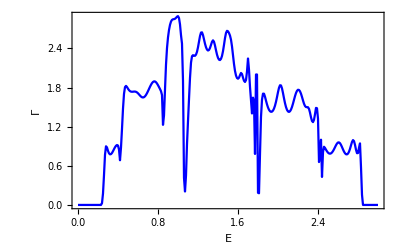

```mathematica
ListLinePlot[trans[0.5],PlotStyle->Blue,Frame->True,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}]
```

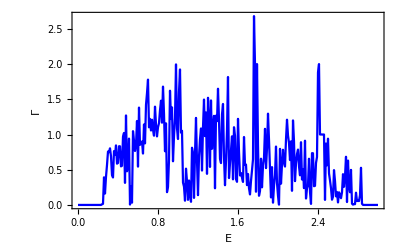

```mathematica
Show[%91,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Ε],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]}]
```

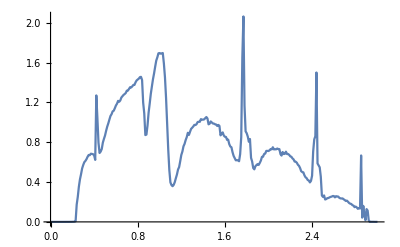

```mathematica
ListLinePlot[%50]
```

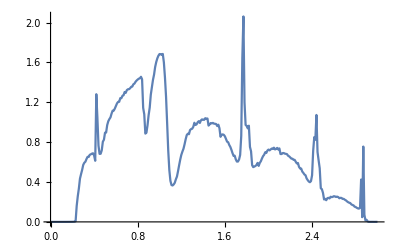

```mathematica
ListLinePlot[%63]
```